## Preamble

```mathematica
NotebookSave[];
Clear["Global`*"];
SetDirectory["/Users/cristian/Documents/Research/Criptography/Notes/Cristian_Orals/Paper"]
<<MaTeX`
<<ToPython`
$Assumptions=ν>0&&ν<1&&h>0&&h<1/2&&γ≥0&&γ<1&&ϵ≥0&&ϵ<1&&δ>0&&δ<1&&_∈Reals
```

/Users/cristian/Documents/Research/Criptography/Notes/Cristian_Orals/Paper

ν>0&&ν<1&&h>0&&h<1/2&&γ≥0&&γ<1&&ϵ≥0&&ϵ<1&&δ>0&&δ<1&&_∈ℝ

## Attacker’s Value of Selfish Mining

Value functions given transition probabilities. Note that here we do not

```mathematica
Val1:=Subscript[V, 0]==ϵ ν Subscript[V, 0]+(1-ϵ)(h ν Subscript[V, 1]+(1-h)ν Subscript[V, 0]);
Val2:=Subscript[V, 1]==ϵ ν Subscript[V, 1]+(1-ϵ)(h ν Subscript[V, 2]+(1-h) ν Subscript[V, c]);
Val3:=Subscript[V, c]==ϵ ν Subscript[V, c]+(1-ϵ)(h 2(1-δ)+(1-h)γ(1-δ)+ ν Subscript[V, 0]);
Val4:=Subscript[V, 2]==ϵ ν Subscript[V, 2]+(1-ϵ)(h ν Subscript[V, 3]+(1-h)(2(1-δ)+ν Subscript[V, 0]));
Val5:=Subscript[V, 3]==ϵ ν Subscript[V, 3]+(1-ϵ)(h ν Subscript[V, 4]+(1-h)(1(1-δ)+ν Subscript[V, 2]));
Val6:=Subscript[V, 4]==ϵ ν Subscript[V, 4]+(1-ϵ)(h ν Subscript[V, 5]+(1-h)(1(1-δ)+ν Subscript[V, 3]));
```

Solve for value functions until V_5 as a function of V_0.

```mathematica
S=Collect[Solve[{Val1,Val2,Val3,Val4,Val5,Val6},{Subscript[V, c],Subscript[V, 1],Subscript[V, 2],Subscript[V, 3],Subscript[V, 4],Subscript[V, 5]}]//Simplify,Subscript[V, 0]];
```

For k≥4 we have that V_k=1/(h ν)V_(k-1)-(1-h)/h V_(k-2)-(1-h)/(h ν). Solve the sequence

```mathematica
SolSeq=RSolve[{V[k]==(1-ϵ ν)/((1-ϵ)h ν)V[k-1]-(1-h)/h V[k-2]-(1-h)/(h ν)(1-δ)},V[k],k, GeneratedParameters->(Subscript[c,#]&)]//Simplify
```

{{V[k]→((-1+h) (-1+δ) (-1+ϵ))/(-1+ν)+2^-k ((h (-1+ϵ) ν)/(-1+ϵ ν+√(1-4 h ν^2+4 h^2 ν^2+(1-2 h)^2 ϵ^2 ν^2-2 ϵ ν (1-4 h ν+4 h^2 ν))))^-k c_1+2^-k ((h (-1+ϵ) ν)/(-1+ϵ ν-√(1-4 h ν^2+4 h^2 ν^2+(1-2 h)^2 ϵ^2 ν^2-2 ϵ ν (1-4 h ν+4 h^2 ν))))^-k c_2}}

Define value function from sequence

```mathematica
SeqVal[k_]=V[k]/.SolSeq[[1]];
```

As we know V_4 and V_5 both from sequence and as functions of V_0, solve for c_1 and c_2 (as functions of V_0).

```mathematica
Cons=Solve[{SeqVal[4]==Subscript[V, 4]/.S[[1]],SeqVal[5]==Subscript[V, 5]/.S[[1]]},{Subscript[c, 1],Subscript[c, 2]}]//Simplify;
```

Note that in the limit from the sequence we have that (for different values of c_2)

```mathematica
DiscreteLimit[SeqVal[n],n->∞,Assumptions->$Assumptions&&Subscript[c, 2]>0]//Factor
DiscreteLimit[SeqVal[n],n->∞,Assumptions->$Assumptions&&Subscript[c, 2]==0]//Factor
DiscreteLimit[SeqVal[n],n->∞,Assumptions->$Assumptions&&Subscript[c, 2]<0]//Factor
```

∞

((-1+h) (-1+δ) (-1+ϵ))/(-1+ν)

-∞

As we know that in the limit V_k→(1-α)/(1-ν), a necessary condition is c_2=0. This pins down the value of V_0.

```mathematica
V0Sol=Solve[0==Subscript[c, 2]/.Cons[[1]],Subscript[V, 0]]//Simplify;
```

Then we define the value of V_0 as a function of the parameters

```mathematica
V0[h_,δ_,ν_,γ_,ϵ_]=Subscript[V, 0]/.V0Sol[[1]]
```

((-1+h) h (-1+δ) (-1+ϵ)^3 ν^2 (2 h^4 (-1+ϵ)^3 ν^3 (-1+ϵ ν)-2 h^3 (-1+ϵ)^2 ν^2 (-1+ϵ ν) √(1-4 h ν^2+4 h^2 ν^2+(1-2 h)^2 ϵ^2 ν^2-2 ϵ ν (1-4 h ν+4 h^2 ν))-h^3 (-1+ϵ)^2 ν^2 (-1+ϵ ν) (-1+ϵ ν-√(1-4 h ν^2+4 h^2 ν^2+(1-2 h)^2 ϵ^2 ν^2-2 ϵ ν (1-4 h ν+4 h^2 ν)))-2 (1-ν) √(1-4 h ν^2+4 h^2 ν^2+(1-2 h)^2 ϵ^2 ν^2-2 ϵ ν (1-4 h ν+4 h^2 ν)) (h^3 (-2+γ) (-1+ϵ)^2 ν^2-h^2 (-1+ϵ) ν (-1+(2+2 γ (-1+ϵ)-ϵ) ν)-γ (-1+ϵ ν)^2+h (-4 (-1+ϵ ν)^2+γ (1+ν^2+2 ϵ^2 ν^2-2 ϵ ν (1+ν))))+(1-ν) (1-ϵ ν+√(1-4 h ν^2+4 h^2 ν^2+(1-2 h)^2 ϵ^2 ν^2-2 ϵ ν (1-4 h ν+4 h^2 ν))) (h^3 (-2+γ) (-1+ϵ)^2 ν^2-h^2 (-1+ϵ) ν (-1+(2+2 γ (-1+ϵ)-ϵ) ν)-γ (-1+ϵ ν)^2+h (-4 (-1+ϵ ν)^2+γ (1+ν^2+2 ϵ^2 ν^2-2 ϵ ν (1+ν))))-2 (1-ν) (1-ϵ ν) (h^3 (-7+2 γ) (-1+ϵ)^2 ν^2-h^2 (-1+ϵ) ν (-1+(6+4 γ (-1+ϵ)-5 ϵ) ν)-γ (-1+ϵ ν)^2+h (-4 (-1+ϵ ν)^2+γ (1+2 ν^2+3 ϵ^2 ν^2-2 ϵ ν (1+2 ν))))))/((-1+ν) (-1+ϵ ν) √(1-4 h ν^2+4 h^2 ν^2+(1-2 h)^2 ϵ^2 ν^2-2 ϵ ν (1-4 h ν+4 h^2 ν)) (-1/(-1+ϵ ν)2 (-1+(1+h (-1+ϵ)+4 ϵ) ν-(h^2 (-1+ϵ)^2+2 ϵ (2+3 ϵ)+h (-1-2 ϵ+3 ϵ^2)) ν^2+(2 h^3 (-1+ϵ)^3+2 ϵ^2 (3+2 ϵ)+3 h ϵ (-1+ϵ^2)+h^2 (2-3 ϵ+ϵ^3)) ν^3-ϵ (-h^2 (-4+ϵ) (-1+ϵ)^2+4 h^3 (-1+ϵ)^3+ϵ^2 (4+ϵ)+h ϵ (-3+2 ϵ+ϵ^2)) ν^4+(h^4 (-1+ϵ)^5+h (-1+ϵ) ϵ^3+ϵ^4+2 h^3 (-1+ϵ)^3 (-1+2 ϵ)-h^2 (-1+ϵ)^2 (1-3 ϵ+ϵ^2)) ν^5)+(2 (-1+(1+h (-1+ϵ)+4 ϵ) ν-2 (h^2 (-1+ϵ)^2+ϵ (2+3 ϵ)+h (-1+ϵ^2)) ν^2+(3 h^3 (-1+ϵ)^3+2 ϵ^2 (3+2 ϵ)+2 h^2 (2-3 ϵ+ϵ^3)+h (-1-3 ϵ+3 ϵ^2+ϵ^3)) ν^3-ϵ (-2 h^2 (-4+ϵ) (-1+ϵ)^2+6 h^3 (-1+ϵ)^3+ϵ^2 (4+ϵ)+2 h (-1+ϵ^2)) ν^4+(h^5 (-1+ϵ)^5+h (-1+ϵ) ϵ^2+ϵ^4+3 h^3 (-1+ϵ)^3 (-1+2 ϵ)-2 h^2 (-1+ϵ)^2 (1-3 ϵ+ϵ^2)) ν^5))/(√(1-4 h ν^2+4 h^2 ν^2+(1-2 h)^2 ϵ^2 ν^2-2 ϵ ν (1-4 h ν+4 h^2 ν)))+((-1+(1+h (-1+ϵ)+4 ϵ) ν-(h^2 (-1+ϵ)^2+2 ϵ (2+3 ϵ)+h (-1-2 ϵ+3 ϵ^2)) ν^2+(2 h^3 (-1+ϵ)^3+2 ϵ^2 (3+2 ϵ)+3 h ϵ (-1+ϵ^2)+h^2 (2-3 ϵ+ϵ^3)) ν^3-ϵ (-h^2 (-4+ϵ) (-1+ϵ)^2+4 h^3 (-1+ϵ)^3+ϵ^2 (4+ϵ)+h ϵ (-3+2 ϵ+ϵ^2)) ν^4+(h^4 (-1+ϵ)^5+h (-1+ϵ) ϵ^3+ϵ^4+2 h^3 (-1+ϵ)^3 (-1+2 ϵ)-h^2 (-1+ϵ)^2 (1-3 ϵ+ϵ^2)) ν^5) (1-ϵ ν+√(1-4 h ν^2+4 h^2 ν^2+(1-2 h)^2 ϵ^2 ν^2-2 ϵ ν (1-4 h ν+4 h^2 ν))))/((-1+ϵ ν) √(1-4 h ν^2+4 h^2 ν^2+(1-2 h)^2 ϵ^2 ν^2-2 ϵ ν (1-4 h ν+4 h^2 ν)))))

## Expected blocks in the blockchain

Probabilities of different states, taken from Eyal and Sirer (2014) (as our transition equations, after some algebra, are equal to theirs). State 3 refers to a hidden branch with 3 OR MORE blocks, and state 0p refers to 0’

```mathematica
Prob0=(1-2h)/(1-4 h^2+2 h^3);
Prob0p=(h (1-h)(1-2h))/(1-4 h^2+2 h^3);
Prob1=(h (1-2h))/(1-4 h^2+2 h^3);
Prob2=h/(1-h) (h(1-2h))/(1-4 h^2+2 h^3);
Prob3=Sum[(h/(1-h))^(k-1)(h(1-2h))/(1-4 h^2+2 h^3),{k,3,∞}];
```

Expected number of blocks added to the blockchain each period is

```mathematica
Σ[h_,ϵ_]=Prob0 (1-ϵ)(1-h)+Prob0p (1-ϵ) 2+Prob1 0+Prob2 (1-ϵ) 2(1-h)+Prob3(1-ϵ)(1-h)//FullSimplify
```

-((1+h (-1+(-2+h) h)) (-1+ϵ))/(1+2 (-2+h) h^2)

```mathematica
Λ[h_]=Σ[h,ϵ]/(1-ϵ)//Simplify
```

(1-h-2 h^2+h^3)/(1-4 h^2+2 h^3)

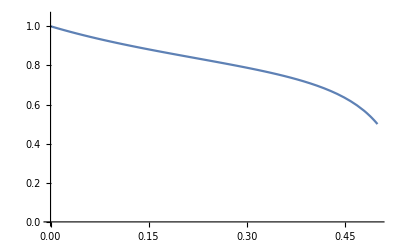

```mathematica
Plot[Λ[h],{h,0,1/2},PlotRange->{{0,1/2},{0,1.05}}]
```

```mathematica
FortranForm[Sqrt[b] a^2]
```

a**2*Sqrt(b)

## Comparison Including Adjusting Difficulty

Define V0 adjusted by using the new length of time periods EB[α] by adjusting the discount factor to ν^EB[α]

```mathematica
V0Adj[h_,δ_,γ_,ϵ_]=V0[h,δ,δ^Λ[h],γ,ϵ]//Simplify;
```

Profitability of selfish mining (over honest mining) is

With Adjustment

```mathematica
ProfAdj[h_,δ_,γ_,ϵ_]=V0Adj[h,δ,γ,ϵ]-(1-ϵ)h;
```

No Adjustment

```mathematica
ProfNA[h_,δ_,γ_,ϵ_]=V0[h,δ,δ,γ,ϵ]-(1-ϵ)h;
```

Analyze Profitability Numerically:

With Adjustment

```mathematica
FunctionRange[{{ProfAdj[h,δ,γ,ϵ]},0<h&&h<1/2&&0<δ&&δ<1&&0<γ&&γ<1&&0<ϵ&&ϵ<1},{h,δ,ϵ,γ},y,WorkingPrecision->MachinePrecision]
```

-0.5≤y≤0.49378

No Adjustment:

```mathematica
FunctionRange[{{ProfNA[h,δ,γ,ϵ]},0<h&&h<1/2&&0<δ&&δ<1&&0<γ&&γ<1&&0<ϵ&&ϵ<1},{h,δ,ϵ,γ},y,WorkingPrecision->MachinePrecision]
```

-0.5≤y≤0.

As selfish mining can be profitable with adjustment, analyze how profitability change with variables:

h

```mathematica
FunctionRange[{{D[ProfAdj[h,δ,γ,ϵ],h]},0<h&&h<1/2&&0<δ&&δ<1&&0<γ&&γ<1&&0<ϵ&&ϵ<1},{h,δ,ϵ,γ},y,WorkingPrecision->MachinePrecision]
```

-0.999987≤y≤9.72061

δ

```mathematica
<<ToMatlab`
CopyToClipboard[ToMatlab[D[ProfAdj[h,δ,γ,ϵ],δ]/.δ->d/.γ->g/.ϵ->e]];
```

γ

```mathematica
FunctionRange[{{D[ProfAdj[h,δ,γ,ϵ],γ]},0<h&&h<1/2&&0<δ&&δ<1&&0<γ&&γ<1&&0<ϵ&&ϵ<1},{h,δ,ϵ,γ},y,WorkingPrecision->MachinePrecision]
```

1.94227×10^-13≤y≤0.109816

ϵ

```mathematica
FunctionRange[{{D[ProfAdj[h,δ,γ,ϵ],ϵ]},0<h&&h<1/2&&0<δ&&δ<1&&0<γ&&γ<1&&0<ϵ&&ϵ<1},{h,δ,ϵ,γ},y,WorkingPrecision->MachinePrecision]
```

-0.499919≤y≤0.5

## Graphs for Profitability of Selfish Mining

Graph Deviation profitability for (γ,ϵ)∈{0,1/2,1}×{0,1/10,1/2}

```mathematica
(* γ=0,ϵ=0 *)
curvegraph=ContourPlot[ProfAdj[h,δ,0,0]==0,{h,0,1/2},{δ,1/2,.999},ContourStyle->Directive[Black,Dashed],BoundaryStyle->None,Frame->True,FrameLabel->(MaTeX[#,Magnification->20/12]&)/@{"h","\\delta"},BaseStyle->{FontFamily->"Latin Modern Roman",FontSize->12}];
shadinggraph1=RegionPlot[ProfAdj[h,δ,0,0]<0,{h,0,1/2},{δ,1/2,.999},PlotStyle->LightGray,BoundaryStyle->None,Frame->True,FrameLabel->(MaTeX[#,Magnification->20/12]&)/@{"h","\\delta"},BaseStyle->{FontFamily->"Latin Modern Roman",FontSize->12}];
shadinggraph2=RegionPlot[ProfAdj[h,δ,0,0]>0,{h,0,1/2},{δ,1/2,.999},PlotStyle->LightGreen,BoundaryStyle->None,Frame->True,FrameLabel->(MaTeX[#,Magnification->20/12]&)/@{"h","\\delta"},BaseStyle->{FontFamily->"Latin Modern Roman",FontSize->12}];
Profit=Show[{shadinggraph1,shadinggraph2,curvegraph}];
Export["sections/Figures/AdjVal_Gamma0_Eps0.pdf",Profit,"pdf"];

(* γ=0,ϵ=1/10 *)
curvegraph=ContourPlot[ProfAdj[h,δ,0,1/10]==0,{h,0,1/2},{δ,1/2,.999},ContourStyle->Directive[Black,Dashed],BoundaryStyle->None,Frame->True,FrameLabel->(MaTeX[#,Magnification->20/12]&)/@{"h","\\delta"},BaseStyle->{FontFamily->"Latin Modern Roman",FontSize->12}];
shadinggraph1=RegionPlot[ProfAdj[h,δ,0,1/10]<0,{h,0,1/2},{δ,1/2,.999},PlotStyle->LightGray,BoundaryStyle->None,Frame->True,FrameLabel->(MaTeX[#,Magnification->20/12]&)/@{"h","\\delta"},BaseStyle->{FontFamily->"Latin Modern Roman",FontSize->12}];
shadinggraph2=RegionPlot[ProfAdj[h,δ,0,1/10]>0,{h,0,1/2},{δ,1/2,.999},PlotStyle->LightGreen,BoundaryStyle->None,Frame->True,FrameLabel->(MaTeX[#,Magnification->20/12]&)/@{"h","\\delta"},BaseStyle->{FontFamily->"Latin Modern Roman",FontSize->12}];
Profit=Show[{shadinggraph1,shadinggraph2,curvegraph}];
Export["sections/Figures/AdjVal_Gamma0_Eps01.pdf",Profit,"pdf"];
(* γ=0,ϵ=1/2 *)
curvegraph=ContourPlot[ProfAdj[h,δ,0,1/2]==0,{h,0,1/2},{δ,1/2,.999},ContourStyle->Directive[Black,Dashed],BoundaryStyle->None,Frame->True,FrameLabel->(MaTeX[#,Magnification->20/12]&)/@{"h","\\delta"},BaseStyle->{FontFamily->"Latin Modern Roman",FontSize->12}];
shadinggraph1=RegionPlot[ProfAdj[h,δ,0,1/2]<0,{h,0,1/2},{δ,1/2,.999},PlotStyle->LightGray,BoundaryStyle->None,Frame->True,FrameLabel->(MaTeX[#,Magnification->20/12]&)/@{"h","\\delta"},BaseStyle->{FontFamily->"Latin Modern Roman",FontSize->12}];
shadinggraph2=RegionPlot[ProfAdj[h,δ,0,1/2]>0,{h,0,1/2},{δ,1/2,.999},PlotStyle->LightGreen,BoundaryStyle->None,Frame->True,FrameLabel->(MaTeX[#,Magnification->20/12]&)/@{"h","\\delta"},BaseStyle->{FontFamily->"Latin Modern Roman",FontSize->12}];
Profit=Show[{shadinggraph1,shadinggraph2,curvegraph}];
Export["sections/Figures/AdjVal_Gamma0_Eps05.pdf",Profit,"pdf"];
(* γ=1/2,ϵ=0 *)
curvegraph=ContourPlot[ProfAdj[h,δ,1/2,0]==0,{h,0,1/2},{δ,1/2,.999},ContourStyle->Directive[Black,Dashed],BoundaryStyle->None,Frame->True,FrameLabel->(MaTeX[#,Magnification->20/12]&)/@{"h","\\delta"},BaseStyle->{FontFamily->"Latin Modern Roman",FontSize->12}];
shadinggraph1=RegionPlot[ProfAdj[h,δ,1/2,0]<0,{h,0,1/2},{δ,1/2,.999},PlotStyle->LightGray,BoundaryStyle->None,Frame->True,FrameLabel->(MaTeX[#,Magnification->20/12]&)/@{"h","\\delta"},BaseStyle->{FontFamily->"Latin Modern Roman",FontSize->12}];
shadinggraph2=RegionPlot[ProfAdj[h,δ,1/2,0]>0,{h,0,1/2},{δ,1/2,.999},PlotStyle->LightGreen,BoundaryStyle->None,Frame->True,FrameLabel->(MaTeX[#,Magnification->20/12]&)/@{"h","\\delta"},BaseStyle->{FontFamily->"Latin Modern Roman",FontSize->12}];
Profit=Show[{shadinggraph1,shadinggraph2,curvegraph}];
Export["sections/Figures/AdjVal_Gamma05_Eps0.pdf",Profit,"pdf"];

(* γ=1/2,ϵ=1/10 *)
curvegraph=ContourPlot[ProfAdj[h,δ,1/2,1/10]==0,{h,0,1/2},{δ,1/2,.999},ContourStyle->Directive[Black,Dashed],BoundaryStyle->None,Frame->True,FrameLabel->(MaTeX[#,Magnification->20/12]&)/@{"h","\\delta"},BaseStyle->{FontFamily->"Latin Modern Roman",FontSize->12}];
shadinggraph1=RegionPlot[ProfAdj[h,δ,1/2,1/10]<0,{h,0,1/2},{δ,1/2,.999},PlotStyle->LightGray,BoundaryStyle->None,Frame->True,FrameLabel->(MaTeX[#,Magnification->20/12]&)/@{"h","\\delta"},BaseStyle->{FontFamily->"Latin Modern Roman",FontSize->12}];
shadinggraph2=RegionPlot[ProfAdj[h,δ,1/2,1/10]>0,{h,0,1/2},{δ,1/2,.999},PlotStyle->LightGreen,BoundaryStyle->None,Frame->True,FrameLabel->(MaTeX[#,Magnification->20/12]&)/@{"h","\\delta"},BaseStyle->{FontFamily->"Latin Modern Roman",FontSize->12}];
Profit=Show[{shadinggraph1,shadinggraph2,curvegraph}];
Export["sections/Figures/AdjVal_Gamma05_Eps01.pdf",Profit,"pdf"];
(* γ=1/2,ϵ=1/2 *)
curvegraph=ContourPlot[ProfAdj[h,δ,1/2,1/2]==0,{h,0,1/2},{δ,1/2,.999},ContourStyle->Directive[Black,Dashed],BoundaryStyle->None,Frame->True,FrameLabel->(MaTeX[#,Magnification->20/12]&)/@{"h","\\delta"},BaseStyle->{FontFamily->"Latin Modern Roman",FontSize->12}];
shadinggraph1=RegionPlot[ProfAdj[h,δ,1/2,1/2]<0,{h,0,1/2},{δ,1/2,.999},PlotStyle->LightGray,BoundaryStyle->None,Frame->True,FrameLabel->(MaTeX[#,Magnification->20/12]&)/@{"h","\\delta"},BaseStyle->{FontFamily->"Latin Modern Roman",FontSize->12}];
shadinggraph2=RegionPlot[ProfAdj[h,δ,1/2,1/2]>0,{h,0,1/2},{δ,1/2,.999},PlotStyle->LightGreen,BoundaryStyle->None,Frame->True,FrameLabel->(MaTeX[#,Magnification->20/12]&)/@{"h","\\delta"},BaseStyle->{FontFamily->"Latin Modern Roman",FontSize->12}];
Profit=Show[{shadinggraph1,shadinggraph2,curvegraph}];
Export["sections/Figures/AdjVal_Gamma05_Eps05.pdf",Profit,"pdf"];
(* γ=1,ϵ=0 *)
curvegraph=ContourPlot[ProfAdj[h,δ,1,0]==0,{h,0,1/2},{δ,1/2,.999},ContourStyle->Directive[Black,Dashed],BoundaryStyle->None,Frame->True,FrameLabel->(MaTeX[#,Magnification->20/12]&)/@{"h","\\delta"},BaseStyle->{FontFamily->"Latin Modern Roman",FontSize->12}];
shadinggraph1=RegionPlot[ProfAdj[h,δ,1,0]<0,{h,0,1/2},{δ,1/2,.999},PlotStyle->LightGray,BoundaryStyle->None,Frame->True,FrameLabel->(MaTeX[#,Magnification->20/12]&)/@{"h","\\delta"},BaseStyle->{FontFamily->"Latin Modern Roman",FontSize->12}];
shadinggraph2=RegionPlot[ProfAdj[h,δ,1,0]>0,{h,0,1/2},{δ,1/2,.999},PlotStyle->LightGreen,BoundaryStyle->None,Frame->True,FrameLabel->(MaTeX[#,Magnification->20/12]&)/@{"h","\\delta"},BaseStyle->{FontFamily->"Latin Modern Roman",FontSize->12}];
Profit=Show[{shadinggraph1,shadinggraph2,curvegraph}];
Export["sections/Figures/AdjVal_Gamma1_Eps0.pdf",Profit,"pdf"];

(* γ=1,ϵ=1/10 *)
curvegraph=ContourPlot[ProfAdj[h,δ,1,1/10]==0,{h,0,1/2},{δ,1/2,.999},ContourStyle->Directive[Black,Dashed],BoundaryStyle->None,Frame->True,FrameLabel->(MaTeX[#,Magnification->20/12]&)/@{"h","\\delta"},BaseStyle->{FontFamily->"Latin Modern Roman",FontSize->12}];
shadinggraph1=RegionPlot[ProfAdj[h,δ,1,1/10]<0,{h,0,1/2},{δ,1/2,.999},PlotStyle->LightGray,BoundaryStyle->None,Frame->True,FrameLabel->(MaTeX[#,Magnification->20/12]&)/@{"h","\\delta"},BaseStyle->{FontFamily->"Latin Modern Roman",FontSize->12}];
shadinggraph2=RegionPlot[ProfAdj[h,δ,1,1/10]>0,{h,0,1/2},{δ,1/2,.999},PlotStyle->LightGreen,BoundaryStyle->None,Frame->True,FrameLabel->(MaTeX[#,Magnification->20/12]&)/@{"h","\\delta"},BaseStyle->{FontFamily->"Latin Modern Roman",FontSize->12}];
Profit=Show[{shadinggraph1,shadinggraph2,curvegraph}];
Export["sections/Figures/AdjVal_Gamma1_Eps01.pdf",Profit,"pdf"];
(* γ=1,ϵ=1/2 *)
curvegraph=ContourPlot[ProfAdj[h,δ,1,1/2]==0,{h,0,1/2},{δ,1/2,.999},ContourStyle->Directive[Black,Dashed],BoundaryStyle->None,Frame->True,FrameLabel->(MaTeX[#,Magnification->20/12]&)/@{"h","\\delta"},BaseStyle->{FontFamily->"Latin Modern Roman",FontSize->12}];
shadinggraph1=RegionPlot[ProfAdj[h,δ,1,1/2]<0,{h,0,1/2},{δ,1/2,.999},PlotStyle->LightGray,BoundaryStyle->None,Frame->True,FrameLabel->(MaTeX[#,Magnification->20/12]&)/@{"h","\\delta"},BaseStyle->{FontFamily->"Latin Modern Roman",FontSize->12}];
shadinggraph2=RegionPlot[ProfAdj[h,δ,1,1/2]>0,{h,0,1/2},{δ,1/2,.999},PlotStyle->LightGreen,BoundaryStyle->None,Frame->True,FrameLabel->(MaTeX[#,Magnification->20/12]&)/@{"h","\\delta"},BaseStyle->{FontFamily->"Latin Modern Roman",FontSize->12}];
Profit=Show[{shadinggraph1,shadinggraph2,curvegraph}];
Export["sections/Figures/AdjVal_Gamma1_Eps05.pdf",Profit,"pdf"];
```

## Case when δ→1 (Everything in Flow Value)

General Case

With Adjustment

```mathematica
V0AdjD1[h_,γ_,ϵ_]=Limit[V0Adj[h,δ,γ,ϵ],δ->1,Direction->"FromBelow"]//Simplify
```

(h (h^2 (9-5 γ)+2 h^3 (-2+γ)+4 h (-1+γ)-γ) (-1+ϵ))/(1-h-2 h^2+h^3)

```mathematica
ProfAdjD1[h_,γ_,ϵ_]=Limit[ProfAdj[h,δ,γ,ϵ],δ->1,Direction->"FromBelow"]//Simplify
```

```mathematica
Reduce[FV0AdjD1[h,γ,ϵ]≥h(1-ϵ)&&$Assumptions,h]
```

_∈ℝ&&0<ν<1&&0≤γ<1&&0≤ϵ<1&&0<δ<1&&(-1+γ)/(-3+2 γ)≤h<1/2

Without Adjustment

```mathematica
FV0D1[h_,γ_,ϵ_]=Limit[V0[h,δ,δ,γ,ϵ],δ->1,Direction->"FromBelow"]//Simplify
```

(h (h^2 (9-5 γ)+2 h^3 (-2+γ)+4 h (-1+γ)-γ) (-1+ϵ))/(1-4 h^2+2 h^3)

```mathematica
Reduce[FV0D1[h,γ,ϵ]>(1-ϵ)h &&$Assumptions,h]
```

False

```mathematica
Assuming[$Assumptions,TrueQ[V0[h,δ,δ,γ,ϵ]≤ (1-ϵ)h]]
```

False

For γ = 0:

Value when difficulty adjusts

```mathematica
V0AdjG0[h_]=Limit[V0Adj[h,δ,0,0],δ->1,Direction->"FromBelow",Assumptions->$Assumptions]//FullSimplify
```

Value when difficulty does not adjust

```mathematica
V0G0[h_]=Limit[(1-δ)V0[α,δ,δ,0,0],δ->1,Direction->"FromBelow",Assumptions->$Assumptions]//Together
```

```mathematica
Plot[{V0G0[h],V0AdjG0[h],h},{h,0,1/2},PlotLegends->"Expressions",PlotStyle->{Red,Blue,{Black,Dashed}}]
```

```mathematica
Reduce[V0AdjG0[h]>h&&h>0&&h<1/2,h]
```

```mathematica
Reduce[V0G0[h]>h&&h>0&&h<1/2,h]
```

For γ = 0.5:

Value when difficulty adjusts

```mathematica
V0AdjGH[h_]=Limit[(1-δ)V0Adj[α,δ,1/2,0],δ->1,Direction->"FromBelow",Assumptions->$Assumptions]//FullSimplify
```

Value when difficulty does not adjust

```mathematica
V0GH[h_]=Limit[(1-δ)V0[α,δ,δ,1/2,0],δ->1,Direction->"FromBelow",Assumptions->$Assumptions]//Together
```

```mathematica
Plot[{V0GH[h],V0AdjGH[h],h},{h,0,1/2},PlotLegends->"Expressions",PlotStyle->{Red,Blue,{Black,Dashed}}]
```

```mathematica
Reduce[V0AdjGH[h]>h&&h>0&&h<1/2,h]
```

```mathematica
Reduce[V0GH[h]>h&&h>0&&h<1/2,h]
```

For γ = 1:

Value when difficulty adjusts

```mathematica
V0AdjG1[h_]=Limit[(1-δ)V0Adj[h,δ,1],δ->1,Direction->"FromBelow",Assumptions->$Assumptions]//FullSimplify
```

Value when difficulty does not adjust

```mathematica
V0G1[h_]=Limit[(1-δ)V0[h,δ,1],δ->1,Direction->"FromBelow",Assumptions->$Assumptions]//Together
```

```mathematica
Plot[{V0G1[h],V0AdjG1[h],h},{h,0,1/2},PlotLegends->"Expressions",PlotStyle->{Red,Blue,{Black,Dashed}}]
```

```mathematica
Reduce[V0AdjG1[h]>h&&h>0&&h<1/2,h]
```

```mathematica
Reduce[V0G1[α]>h&&h>0&&h<1/2,h]
```